```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
<<Superradiance`SWSH`
```

```mathematica
Spectral0[𝓈_,ℓ_,𝓂_,𝒸_]:=Module[{l0,delta,lf,nC,sp},
nC=Ceiling[5*Sqrt[Log[Abs[𝒸]^3+1] Abs[𝒸]]+14];
	delta=Ceiling[(nC+ℓ-MaxAbs[𝓂,𝓈])/2];
	lf=delta+ℓ;
	l0=Max[ℓ-delta,MaxAbs[𝓂,𝓈]]-1;
Print[l0+1,lf];
sp=SparseArray[{
{i_,i_}:>-If[i+l0==ℓ,Style[Subscript[Ev0, i+l0],Red],Subscript[Ev0, i+l0]],
{i_,j_}/;Abs[j-i]==1:>Subscript[Ev1, {l0+i,l0+j}],
{i_,j_}/;Abs[j-i]==2:>Subscript[Ev2, {l0+i,l0+j}]},
{lf-l0,lf-l0}]
]
Normal@Spectral0[-2,50,25,5.00]
```

2582

```mathematica
Range[-25]
```

{}

```mathematica
Spectral[-2,50,25,5.00]//Chop
```

-0.991331

{2540.18,{{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,-8.11729×10^-10},{42,3.87943×10^-9},{43,1.56413×10^-7},{44,-1.01343×10^-6},{45,-0.000022008},{46,0.000176746},{47,0.00202681},{48,-0.0191585},{49,-0.092634},{50,0.991331},{51,0.0870607},{52,0.0269606},{53,0.00215509},{54,0.000361509},{55,0.0000264434},{56,3.19068×10^-6},{57,2.15401×10^-7},{58,2.08654×10^-8},{59,1.30994×10^-9},{60,1.07867×10^-10},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,0},{68,0},{69,0},{70,0},{71,0},{72,0},{73,0},{74,0},{75,0},{76,0},{77,0},{78,0},{79,0},{80,0},{81,0},{82,0}}}

```mathematica
tb1=ParallelTable[With[{S=SpinWeightedSpheroidalHarmonicS[-1,50,25,c]},Table[{c,θ,S[π xθ,0]},{xθ,0.,1.,0.004}]],{c,0,3,0.002}]
```

```mathematica
tb0=tb1//Flatten[#,1]&
```

{{0.,0.,0.},{0.,0.0125664,-5.42245×10^-43},{0.,0.0251327,-9.06703×10^-36},{0.,0.0376991,-1.51788×10^-31},{0.,0.0502655,-1.501×10^-28},{0.,0.0628319,-3.14678×10^-26},75539,{3.,3.07876,-1.06649×10^-24},{3.,3.09133,-3.28821×10^-27},{3.,3.10389,-1.88489×10^-30},{3.,3.11646,-5.03179×10^-35},{3.,3.12903,-7.5479×10^-43},{3.,3.14159,0.}}
 |  |  |  |

-0.999897

General::munfl: (6.12323×10^-17)^28 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.12323×10^-17)^30 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.12323×10^-17)^32 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-0.999979

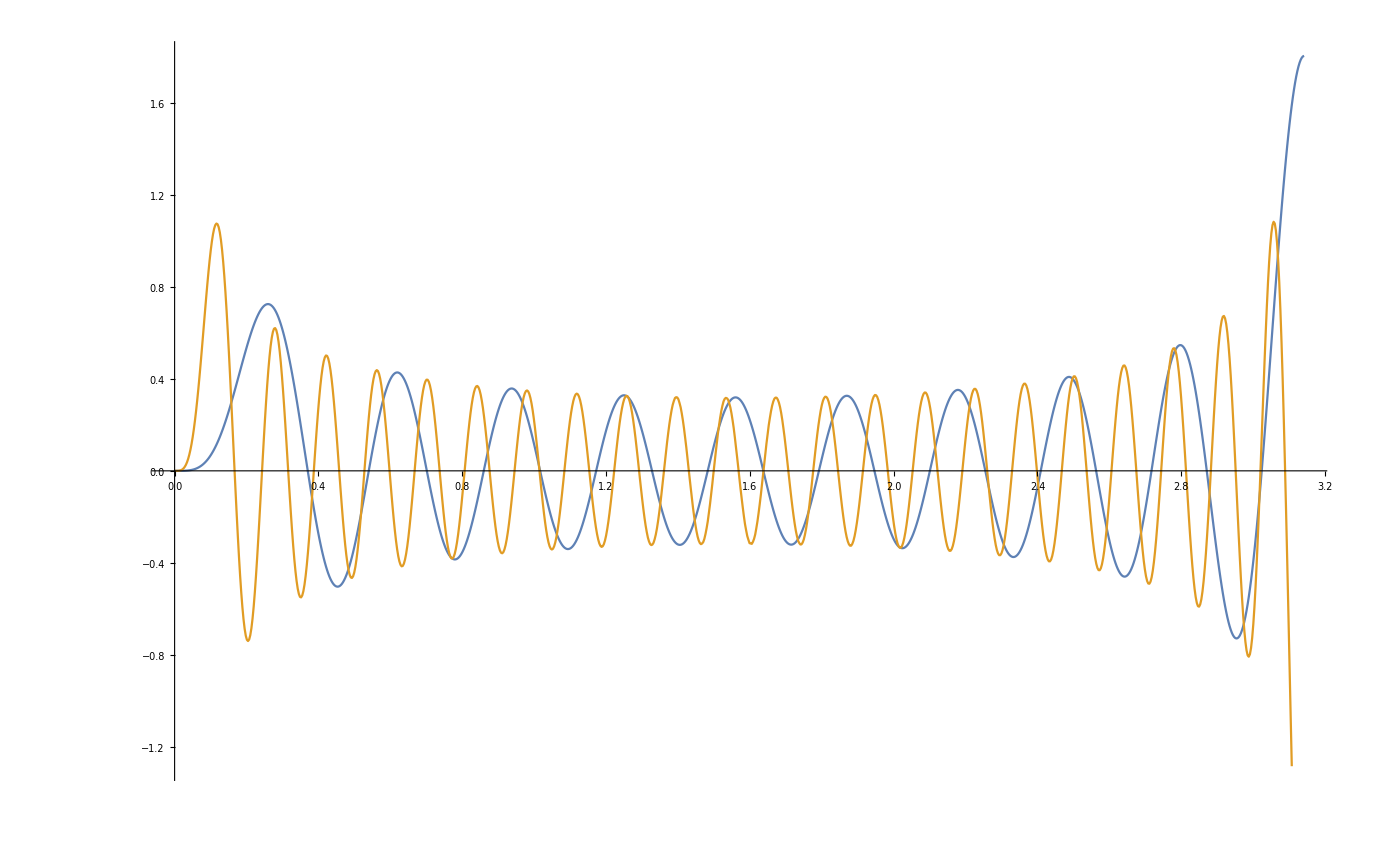

```mathematica
Chop@With[{S=SpinWeightedSpheroidalHarmonicS[-2,#,-2,0.7*0.3]},Table[{xθ π,S[xθ π,0]},{xθ,0.,1.,0.001}]]&/@{20,45}//ListPlot[#,Joined->True]&
```

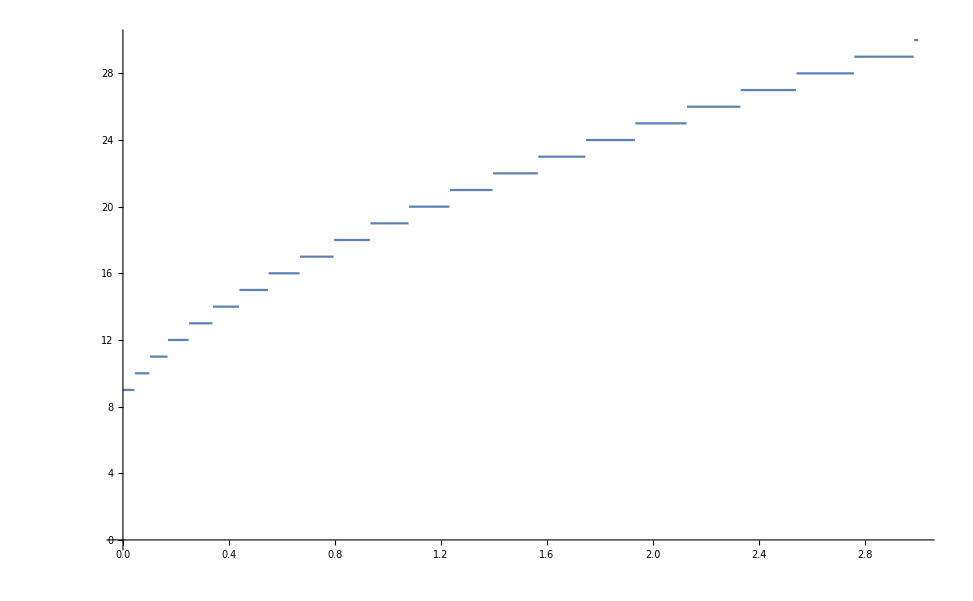

```mathematica
Plot[Ceiling[6Sqrt[Log[20Abs[𝒸]+1] Abs[𝒸]]+8],{𝒸,0,3},PlotRange->{0,Automatic}]
```